```mathematica
(1-x)^2(1/((1-x)+(1-z))-1/((1-x)+(1-y)))+x^2(1/(x+z)-1/(x+y))-(1/(1+1-z)-1/(1+1-y))//FullSimplify
```

1/(2-y)+1/(-2+z)-((-1+x)^2 (y-z))/((-2+x+y) (-2+x+z))+x^2 (-1/(x+y)+1/(x+z))

```mathematica
%//FullSimplify//Factor
```

-((x (y-z) (x^3-2 x^2 y z+6 x^2 y+6 x^2 z-12 x^2+x y^2+7 x y z-12 x y+x z^2-12 x z+16 x+2 y^2 z^2-3 y^2 z-3 y z^2+4 y z))/((y-2) (z-2) (x+y-2) (x+y) (x+z-2) (x+z)))

```mathematica
%63
```

```mathematica
-((x (y-z) (16 x-12 x^2+x^3-12 x y+6 x^2 y+x y^2-12 x z+6 x^2 z+4 y z+7 x y z-2 x^2 y z-3 y^2 z+x z^2-3 y z^2+2 y^2 z^2))/((-1) (-1) (+1) (-1) (-1) (+1)))//FullSimplify
```

-x (y-z) (x^3-2 x^2 (6+y (-3+z)-3 z)+y z (4-3 z+y (-3+2 z))+x (16+y^2+(-12+z) z+y (-12+7 z)))

```mathematica
%//Factor
```

```mathematica
-(y-z) (16 x-12 x^2+x^3-12 x y+6 x^2 y+x y^2-12 x z+6 x^2 z+4 y z+7 x y z-2 x^2 y z-3 y^2 z+x z^2-3 y z^2+2 y^2 z^2)//FullSimplify
```

(-y+z) (x^3-2 x^2 (6+y (-3+z)-3 z)+y z (4-3 z+y (-3+2 z))+x (16+y^2+(-12+z) z+y (-12+7 z)))

```mathematica
(16 x-12 x^2+x^3-12 x y+6 x^2 y+x y^2-12 x z+6 x^2 z+4 y z+7 x y z-2 x^2 y z-3 y^2 z+x z^2-3 y z^2+2 y^2 z^2)/.z->(y+a)//FullSimplify//Factor
```

```mathematica
%69//FullSimplify
```

x^3-2 x^2 (6+a (-3+y)+(-6+y) y)+y (a+y) (4-3 a+2 (-3+a) y+2 y^2)+x (a^2+(4-3 y)^2+3 a (-4+3 y))

```mathematica
(x^3-2 x^2 (6+y (-3+z)-3 z)+y z (4-3 z+y (-3+2 z))+x (16+y^2+(-12+z) z+y (-12+7 z)))//FullSimplify
```

x^3-2 x^2 (6+y (-3+z)-3 z)+y z (4-3 z+y (-3+2 z))+x (16+y^2+(-12+z) z+y (-12+7 z))

```mathematica
(1-x)^2(1/((1-x)+(1-z))-1/((1-x)+(1-y)))+x^2(1/(x+z)-1/(x+y))-(1/(1+1-z)-1/(1+1-y))==0//FullSimplify
```

1/(2-y)+1/(-2+z)+x^2 (-1/(x+y)+1/(x+z))==((-1+x)^2 (y-z))/((-2+x+y) (-2+x+z))

```mathematica
t=Table[(1-x)^2(1/((1-x)+(1-z))-1/((1-x)+(1-y)))+x^2(1/(x+z)-1/(x+y))-(1/(1+1-z)-1/(1+1-y)),{z,.01,.99,.01},{y,.01,z-.01,.01},{x,.01,y-.01,.01}];
```

```mathematica
Min[Flatten@t]
```

-0.16106

```mathematica
Max[Flatten@t]
```

-3.90274×10^-6

```mathematica
(1-x)^2(1/((1-x)+(1-z))-1/((1-x)+(1-y)))+x^2(1/(x+z)-1/(x+y))-(1/(1+1-z)-1/(1+1-y))/.{z->y+b}/.{y->x+a}//FullSimplify//Factor
```

```mathematica
-((b x (4 a^2-6 a^3+2 a^4+4 a b-9 a^2 b+4 a^3 b-3 a b^2+2 a^2 b^2+16 x-16 a x-9 a^2 x+8 a^3 x-8 b x-9 a b x+12 a^2 b x-2 b^2 x+4 a b^2 x-32 x^2+12 a x^2+10 a^2 x^2+6 b x^2+10 a b x^2+2 b^2 x^2+16 x^3+4 a x^3+2 b x^3))/((-1) (-1) (-1) (1) (-1) (1)))//FullSimplify//Factor
```

-b x (4 a^2-6 a^3+2 a^4+4 a b-9 a^2 b+4 a^3 b-3 a b^2+2 a^2 b^2+16 x-16 a x-9 a^2 x+8 a^3 x-8 b x-9 a b x+12 a^2 b x-2 b^2 x+4 a b^2 x-32 x^2+12 a x^2+10 a^2 x^2+6 b x^2+10 a b x^2+2 b^2 x^2+16 x^3+4 a x^3+2 b x^3)

```mathematica
-(4 a^2-6 a^3+2 a^4+4 a b-9 a^2 b+4 a^3 b-3 a b^2+2 a^2 b^2+16 x-16 a x-9 a^2 x+8 a^3 x-8 b x-9 a b x+12 a^2 b x-2 b^2 x+4 a b^2 x-32 x^2+12 a x^2+10 a^2 x^2+6 b x^2+10 a b x^2+2 b^2 x^2+16 x^3+4 a x^3+2 b x^3)//FullSimplify
```

-a (a+b) (4-3 b+2 a (-3+a+b))-16 x+(-8 a^3+a^2 (9-12 b)+2 b (4+b)+a (16+(9-4 b) b)) x-2 (-16+5 a^2+b (3+b)+a (6+5 b)) x^2-2 (8+2 a+b) x^3

```mathematica
(1-x)^2(1/((1-x)+(1-z))-1/((1-x)+(1-y)))+x^2(1/(x+z)-1/(x+y))/.x->0
```

-1/(2-y)+1/(2-z)

```mathematica
D[(1-x)^2(1/((1-x)+(1-z))-1/((1-x)+(1-y)))+x^2(1/(x+z)-1/(x+y)),x]
```

(1-x)^2 (-1/(2-x-y)^2+1/(2-x-z)^2)-2 (1-x) (-1/(2-x-y)+1/(2-x-z))+x^2 (1/(x+y)^2-1/(x+z)^2)+2 x (-1/(x+y)+1/(x+z))

```mathematica
%//FullSimplify
```

((x-y) (y (-3+2 y)+x (-1+2 y)))/((-2+x+y)^2 (x+y)^2)+(-1+x)^2/(-2+x+z)^2-(2 (-1+x))/(-2+x+z)-x^2/(x+z)^2+(2 x)/(x+z)

```mathematica
%/.x->0
```

-(-3+2 y)/(-2+y)^2+1/(-2+z)^2+2/(-2+z)

```mathematica
D[x/(x+z)+1/(z-2),z]
```

-1/(-2+z)^2-x/(x+z)^2

```mathematica
D[x/(x+z)-1/(1+z),z]
```

1/(1+z)^2-x/(x+z)^2

```mathematica
D[x/(x+z)^2,x]
```

-(2 x)/(x+z)^3+1/(x+z)^2

```mathematica
Solve[%==0]
```

{{z→x}}

```mathematica
D[-(2 x)/(x+z)^3+1/(x+z)^2,x]
```

(6 x)/(x+z)^4-4/(x+z)^3

```mathematica
%/.x->z
```

-1/(8 z^3)

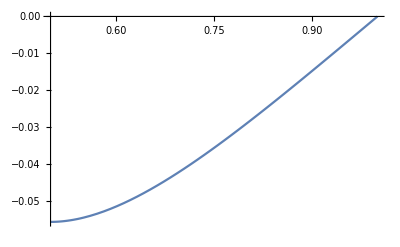

```mathematica
Plot[1/(1+z)^2-x/(x+z)^2/.z->.5,{x,.5,1}]
```

```mathematica
(1-x)^2(1/((1-x)+(1-z))-1/((1-x)+(1-y)))+x^2(1/(x+z)-1/(x+y))-(1/(1+1-z)-1/(1+1-y))<0//FullSimplify
```

1/(2-y)+1/(-2+z)+x^2 (-1/(x+y)+1/(x+z))<((-1+x)^2 (y-z))/((-2+x+y) (-2+x+z))